# Jeremy — PS 2 — 2025-01-21

### Exercises from EIWL3 Section 5

```mathematica
Reverse[Table[n^2,{n,10}]]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
Total[Table[n^2,{n,10}]]
```

385

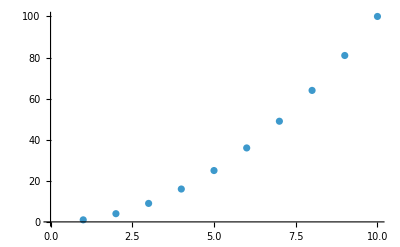

```mathematica
ListPlot[Table[n^2,{n,10}]]
```

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Sort[Join[Table[n^2,{n,5}],Table[n^3,{n,5}]]]
```

{1,1,4,8,9,16,25,27,64,125}

```mathematica
Length[IntegerDigits[2^128]]
```

39

```mathematica
First[IntegerDigits[2^32]]
```

4

```mathematica
Table[Part[IntegerDigits[2^100],n],{n,10}]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
Last[Sort[IntegerDigits[2^20]]]
```

8

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

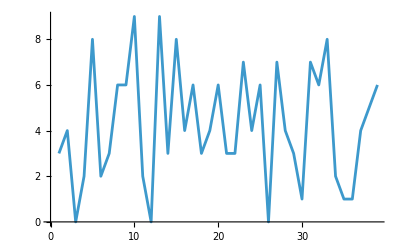

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

```mathematica
Drop[Take[Range[100],20],10]
```

{11,12,13,14,15,16,17,18,19,20}

### Exercises from EIWL3 Section 6

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

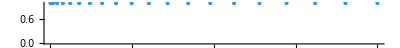

```mathematica
NumberLinePlot[Table[n^2,{n,20}]]
```

```mathematica
Table[n*2,{n,10}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[n,{n,10}]
```

{1,2,3,4,5,6,7,8,9,10}

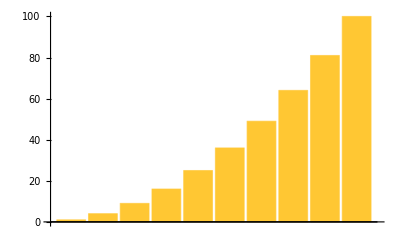

```mathematica
BarChart[Table[n^2,{n,10}]]
```

```mathematica
Table[IntegerDigits[n^2],{n,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

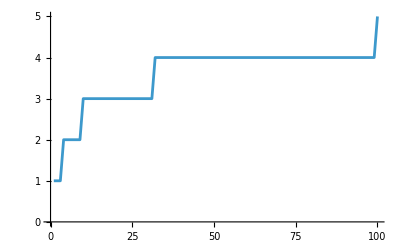

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,100}]]
```

```mathematica
Table[Part[IntegerDigits[n^2],1],{n,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

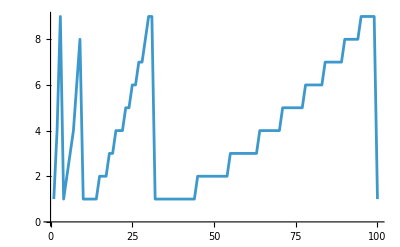

```mathematica
ListLinePlot[Table[Part[IntegerDigits[n^2],1],{n,100}]]
```

### Exercises from EIWL3 Section 7

```mathematica
{Red,Yellow,Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Column[{Red,Yellow,Green}]
```

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

```mathematica
ColorNegate[Orange]
```

RGBColor[0., 0.5, 1.]

```mathematica
Table[Hue[n],{n,0,1,0.02}]
```

{Hue[0.],Hue[0.02],Hue[0.04],Hue[0.06],Hue[0.08],Hue[0.1],Hue[0.12],Hue[0.14],Hue[0.16],Hue[0.18],Hue[0.2],Hue[0.22],Hue[0.24],Hue[0.26],Hue[0.28],Hue[0.3],Hue[0.32],Hue[0.34],Hue[0.36],Hue[0.38],Hue[0.4],Hue[0.42],Hue[0.44],Hue[0.46],Hue[0.48],Hue[0.5],Hue[0.52],Hue[0.54],Hue[0.56],Hue[0.58],Hue[0.6],Hue[0.62],Hue[0.64],Hue[0.66],Hue[0.68],Hue[0.7000000000000001],Hue[0.72],Hue[0.74],Hue[0.76],Hue[0.78],Hue[0.8],Hue[0.8200000000000001],Hue[0.84],Hue[0.86],Hue[0.88],Hue[0.9],Hue[0.92],Hue[0.9400000000000001],Hue[0.96],Hue[0.98],Hue[1.]}

```mathematica
Table[RGBColor[1,n,1],{n,0,1,0.05}]
```

{RGBColor[1, 0., 1],RGBColor[1, 0.05, 1],RGBColor[1, 0.1, 1],RGBColor[1, 0.15000000000000002, 1],RGBColor[1, 0.2, 1],RGBColor[1, 0.25, 1],RGBColor[1, 0.30000000000000004, 1],RGBColor[1, 0.35000000000000003, 1],RGBColor[1, 0.4, 1],RGBColor[1, 0.45, 1],RGBColor[1, 0.5, 1],RGBColor[1, 0.55, 1],RGBColor[1, 0.6000000000000001, 1],RGBColor[1, 0.65, 1],RGBColor[1, 0.7000000000000001, 1],RGBColor[1, 0.75, 1],RGBColor[1, 0.8, 1],RGBColor[1, 0.8500000000000001, 1],RGBColor[1, 0.9, 1],RGBColor[1, 0.9500000000000001, 1],RGBColor[1, 1., 1]}

```mathematica
Blend[{Pink,Yellow}]
```

RGBColor[1, 0.75, 0.25]

```mathematica
Table[Blend[{Yellow,Hue[n]}],{n,0,1,0.05}]
```

{RGBColor[1., 0.5, 0.],RGBColor[1., 0.65, 0.],RGBColor[1., 0.8, 0.],RGBColor[1., 0.9500000000000001, 0.],RGBColor[0.8999999999999999, 1., 0.],RGBColor[0.75, 1., 0.],RGBColor[0.5999999999999999, 1., 0.],RGBColor[0.5, 1., 0.050000000000000044],RGBColor[0.5, 1., 0.20000000000000018],RGBColor[0.5, 1., 0.3500000000000001],RGBColor[0.5, 1., 0.5],RGBColor[0.5, 0.8499999999999999, 0.5],RGBColor[0.5, 0.6999999999999997, 0.5],RGBColor[0.5, 0.5499999999999998, 0.5],RGBColor[0.6000000000000001, 0.5, 0.5],RGBColor[0.75, 0.5, 0.5],RGBColor[0.9000000000000004, 0.5, 0.5],RGBColor[1., 0.5, 0.44999999999999973],RGBColor[1., 0.5, 0.2999999999999998],RGBColor[1., 0.5, 0.1499999999999999],RGBColor[1., 0.5, 0.]}

```mathematica
Table[{n,Hue[n]},{n,0,1,0.1}]
```

{{0.,Hue[0.]},{0.1,Hue[0.1]},{0.2,Hue[0.2]},{0.3,Hue[0.30000000000000004]},{0.4,Hue[0.4]},{0.5,Hue[0.5]},{0.6,Hue[0.6000000000000001]},{0.7,Hue[0.7000000000000001]},{0.8,Hue[0.8]},{0.9,Hue[0.9]},{1.,Hue[1.]}}

```mathematica
Style[Purple,100]
```

RGBColor[0.5, 0, 0.5]

```mathematica
Table[Style[Red,n],{n,10,100,10}]
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

```mathematica
Style[Style[999,Red],100]
```

999

```mathematica
Table[Style[n^2,n^2],{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[Part[{Red, Yellow, Green},RandomInteger[2]+1],100]
```

{RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0]}

```mathematica
Table[Style[Part[IntegerDigits[2^1000],n],3*Part[IntegerDigits[2^1000],n]],{n,50}]
```

{1,0,7,1,5,0,8,6,0,7,1,8,6,2,6,7,3,2,0,9,4,8,4,2,5,0,4,9,0,6,0,0,0,1,8,1,0,5,6,1,4,0,4,8,1,1,7,0,5,5}

### Exercises from EIWL3 Section 8



```mathematica
Graphics[RegularPolygon[3]]
```

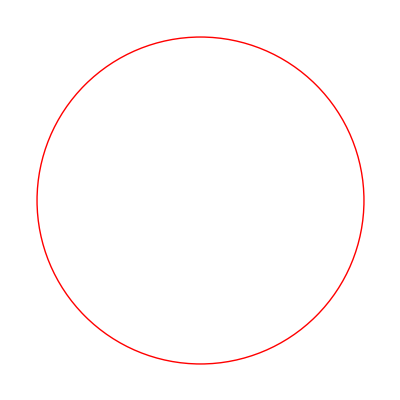

```mathematica
Graphics[Style[Circle[],Red]]
```

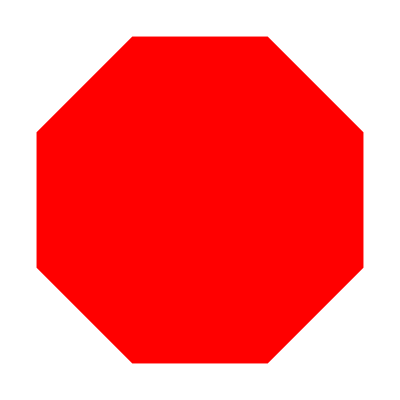

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```


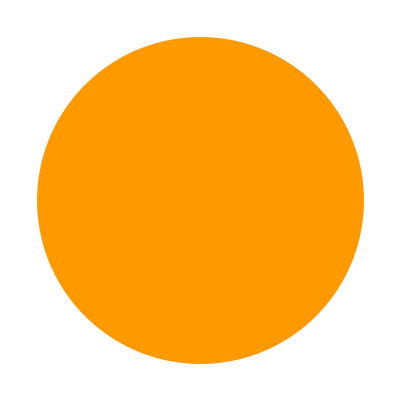
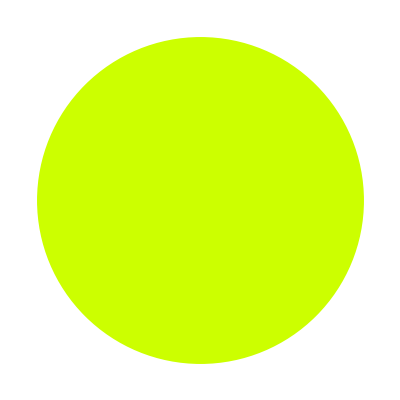
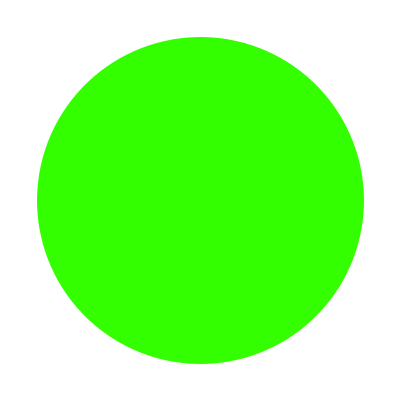
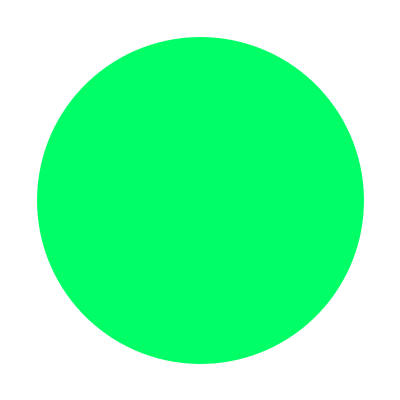
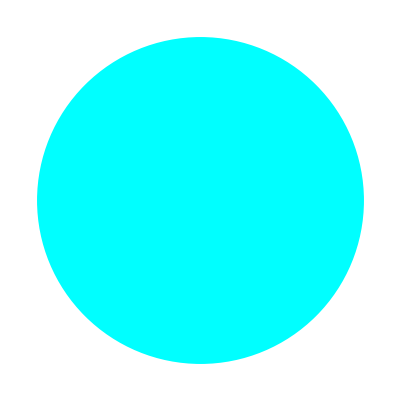
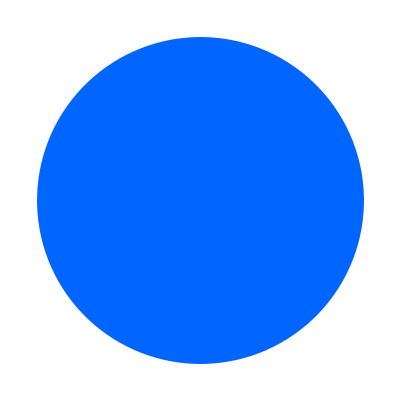
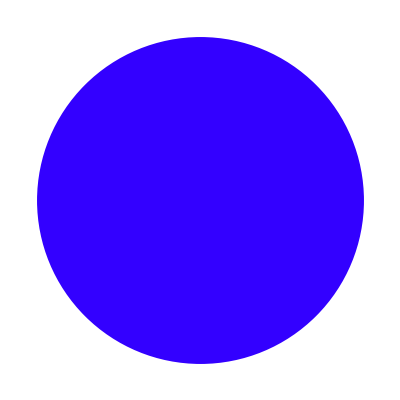
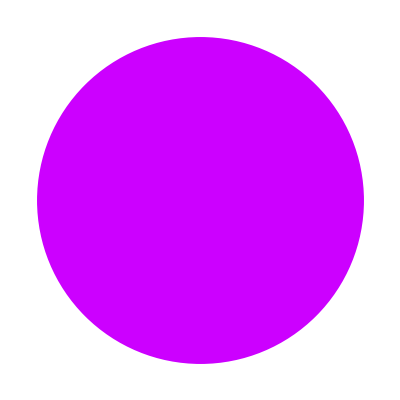
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[],Hue[n]]],{n,0,1,0.1}]
```

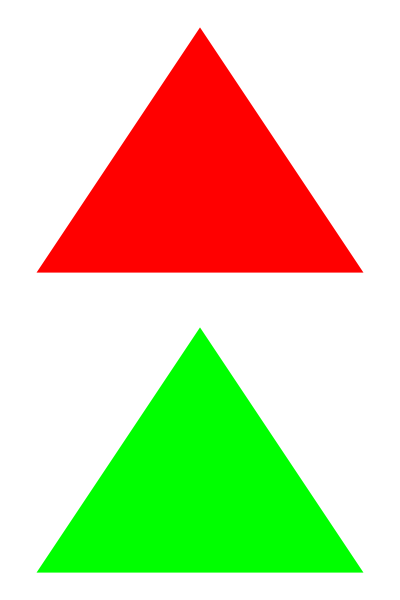

```mathematica
Column[{Graphics[Style[RegularPolygon[3],Red]],Graphics[Style[RegularPolygon[3],Green]]}]
```

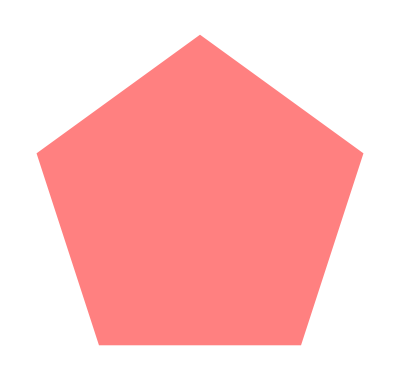
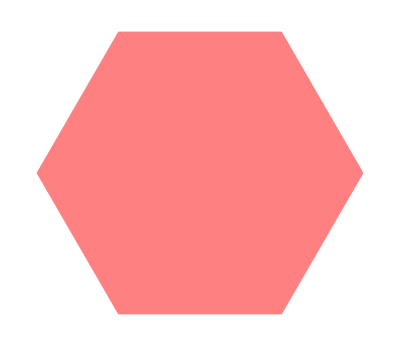
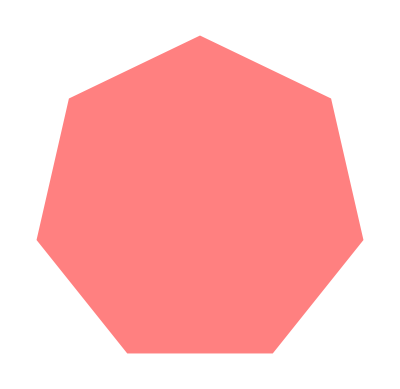
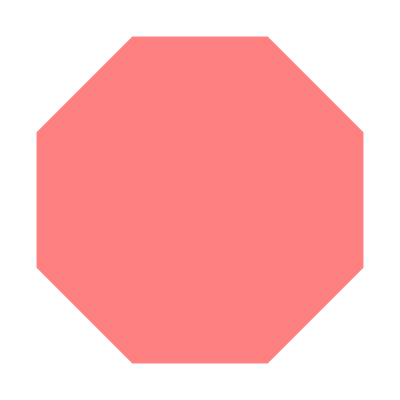
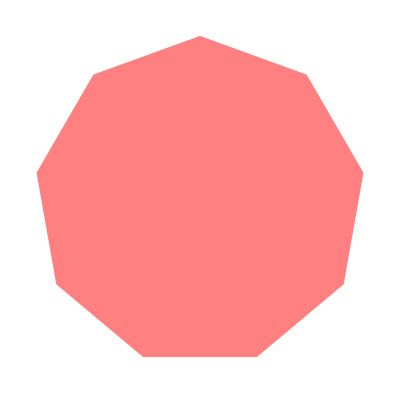
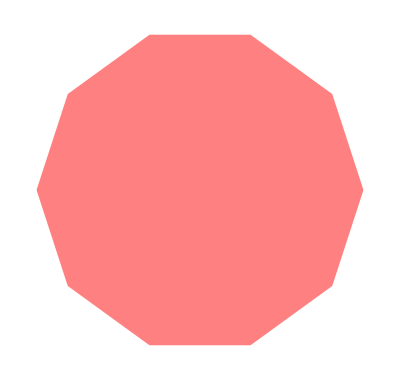

```mathematica
Table[Graphics[Style[RegularPolygon[n],Pink]],{n,5,10}]
```

```mathematica
Graphics3D[Style[Cylinder[],Purple]]
```

-Graphics3D-

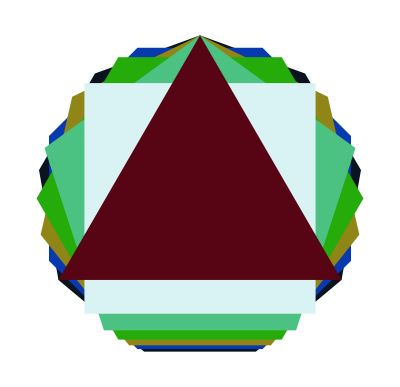

```mathematica
Graphics[Table[Style[RegularPolygon[9-n],RandomColor[]],{n,0,6}]]
```